# Edgeworth Expansion For Asian Option Pricing

## Coefficients of Edgeworth Expansion

```mathematica
Clear[dcum, r, d];
(* 
用已知分布 fx 來逼近未知分布 fy，
list dcum 代表 cumulants of 
*)
ini=TimeUsed[];
k=12;
Series[ⅇ^x, {x, 0, k}]//Normal;
%/.x->Sum[dcum[[r]](-d)^r/(r!), {r, 1, k}];
Take[CoefficientList[%, d], k+1](-1)^Range[0, k] Range[0, k]!//Simplify

TimeUsed[]-ini

(* Symbolic 的算要算很久，展 10 項花 3 秒，12 項 64 秒 *)
(* 第零到四項和 Jarrow 論文上寫的一樣，但和 Wakeman 寫的不一樣 *)
%%//TableForm
```

Part::partd: Part specification dcum ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification dcum ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification dcum ⟦ 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

{1,dcum⟦1⟧,dcum⟦1⟧^2+dcum⟦2⟧,dcum⟦1⟧^3+3 dcum⟦1⟧ dcum⟦2⟧+dcum⟦3⟧,dcum⟦1⟧^4+6 dcum⟦1⟧^2 dcum⟦2⟧+3 dcum⟦2⟧^2+4 dcum⟦1⟧ dcum⟦3⟧+dcum⟦4⟧,dcum⟦1⟧^5+10 dcum⟦1⟧^3 dcum⟦2⟧+10 dcum⟦1⟧^2 dcum⟦3⟧+10 dcum⟦2⟧ dcum⟦3⟧+5 dcum⟦1⟧ (3 dcum⟦2⟧^2+dcum⟦4⟧)+dcum⟦5⟧,dcum⟦1⟧^6+15 dcum⟦1⟧^4 dcum⟦2⟧+15 dcum⟦2⟧^3+20 dcum⟦1⟧^3 dcum⟦3⟧+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+15 dcum⟦1⟧^2 (3 dcum⟦2⟧^2+dcum⟦4⟧)+6 dcum⟦1⟧ (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+dcum⟦6⟧,dcum⟦1⟧^7+21 dcum⟦1⟧^5 dcum⟦2⟧+35 dcum⟦1⟧^4 dcum⟦3⟧+105 dcum⟦2⟧^2 dcum⟦3⟧+35 dcum⟦3⟧ dcum⟦4⟧+35 dcum⟦1⟧^3 (3 dcum⟦2⟧^2+dcum⟦4⟧)+21 dcum⟦2⟧ dcum⟦5⟧+21 dcum⟦1⟧^2 (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+7 dcum⟦1⟧ (15 dcum⟦2⟧^3+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+dcum⟦6⟧)+dcum⟦7⟧,dcum⟦1⟧^8+28 dcum⟦1⟧^6 dcum⟦2⟧+105 dcum⟦2⟧^4+56 dcum⟦1⟧^5 dcum⟦3⟧+210 dcum⟦2⟧^2 dcum⟦4⟧+35 dcum⟦4⟧^2+70 dcum⟦1⟧^4 (3 dcum⟦2⟧^2+dcum⟦4⟧)+56 dcum⟦3⟧ dcum⟦5⟧+56 dcum⟦1⟧^3 (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+28 dcum⟦2⟧ (10 dcum⟦3⟧^2+dcum⟦6⟧)+28 dcum⟦1⟧^2 (15 dcum⟦2⟧^3+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+dcum⟦6⟧)+8 dcum⟦1⟧ (105 dcum⟦2⟧^2 dcum⟦3⟧+35 dcum⟦3⟧ dcum⟦4⟧+21 dcum⟦2⟧ dcum⟦5⟧+dcum⟦7⟧)+dcum⟦8⟧,dcum⟦1⟧^9+36 dcum⟦1⟧^7 dcum⟦2⟧+84 dcum⟦1⟧^6 dcum⟦3⟧+1260 dcum⟦2⟧^3 dcum⟦3⟧+280 dcum⟦3⟧^3+126 dcum⟦1⟧^5 (3 dcum⟦2⟧^2+dcum⟦4⟧)+378 dcum⟦2⟧^2 dcum⟦5⟧+126 dcum⟦4⟧ dcum⟦5⟧+126 dcum⟦1⟧^4 (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+84 dcum⟦3⟧ dcum⟦6⟧+84 dcum⟦1⟧^3 (15 dcum⟦2⟧^3+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+dcum⟦6⟧)+36 dcum⟦2⟧ (35 dcum⟦3⟧ dcum⟦4⟧+dcum⟦7⟧)+36 dcum⟦1⟧^2 (105 dcum⟦2⟧^2 dcum⟦3⟧+35 dcum⟦3⟧ dcum⟦4⟧+21 dcum⟦2⟧ dcum⟦5⟧+dcum⟦7⟧)+9 dcum⟦1⟧ (105 dcum⟦2⟧^4+210 dcum⟦2⟧^2 dcum⟦4⟧+35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+28 dcum⟦2⟧ (10 dcum⟦3⟧^2+dcum⟦6⟧)+dcum⟦8⟧)+dcum⟦9⟧,dcum⟦1⟧^10+45 dcum⟦1⟧^8 dcum⟦2⟧+945 dcum⟦2⟧^5+120 dcum⟦1⟧^7 dcum⟦3⟧+3150 dcum⟦2⟧^3 dcum⟦4⟧+2100 dcum⟦3⟧^2 dcum⟦4⟧+210 dcum⟦1⟧^6 (3 dcum⟦2⟧^2+dcum⟦4⟧)+126 dcum⟦5⟧^2+252 dcum⟦1⟧^5 (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+210 dcum⟦4⟧ dcum⟦6⟧+630 dcum⟦2⟧^2 (10 dcum⟦3⟧^2+dcum⟦6⟧)+210 dcum⟦1⟧^4 (15 dcum⟦2⟧^3+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+dcum⟦6⟧)+120 dcum⟦3⟧ dcum⟦7⟧+120 dcum⟦1⟧^3 (105 dcum⟦2⟧^2 dcum⟦3⟧+35 dcum⟦3⟧ dcum⟦4⟧+21 dcum⟦2⟧ dcum⟦5⟧+dcum⟦7⟧)+45 dcum⟦2⟧ (35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+dcum⟦8⟧)+45 dcum⟦1⟧^2 (105 dcum⟦2⟧^4+210 dcum⟦2⟧^2 dcum⟦4⟧+35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+28 dcum⟦2⟧ (10 dcum⟦3⟧^2+dcum⟦6⟧)+dcum⟦8⟧)+10 dcum⟦1⟧ (1260 dcum⟦2⟧^3 dcum⟦3⟧+280 dcum⟦3⟧^3+378 dcum⟦2⟧^2 dcum⟦5⟧+126 dcum⟦4⟧ dcum⟦5⟧+84 dcum⟦3⟧ dcum⟦6⟧+36 dcum⟦2⟧ (35 dcum⟦3⟧ dcum⟦4⟧+dcum⟦7⟧)+dcum⟦9⟧)+dcum⟦10⟧,dcum⟦1⟧^11+55 dcum⟦1⟧^9 dcum⟦2⟧+165 dcum⟦1⟧^8 dcum⟦3⟧+17325 dcum⟦2⟧^4 dcum⟦3⟧+5775 dcum⟦3⟧ dcum⟦4⟧^2+330 dcum⟦1⟧^7 (3 dcum⟦2⟧^2+dcum⟦4⟧)+6930 dcum⟦2⟧^3 dcum⟦5⟧+4620 dcum⟦3⟧^2 dcum⟦5⟧+462 dcum⟦1⟧^6 (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+462 dcum⟦5⟧ dcum⟦6⟧+462 dcum⟦1⟧^5 (15 dcum⟦2⟧^3+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+dcum⟦6⟧)+330 dcum⟦4⟧ dcum⟦7⟧+990 dcum⟦2⟧^2 (35 dcum⟦3⟧ dcum⟦4⟧+dcum⟦7⟧)+330 dcum⟦1⟧^4 (105 dcum⟦2⟧^2 dcum⟦3⟧+35 dcum⟦3⟧ dcum⟦4⟧+21 dcum⟦2⟧ dcum⟦5⟧+dcum⟦7⟧)+165 dcum⟦3⟧ dcum⟦8⟧+165 dcum⟦1⟧^3 (105 dcum⟦2⟧^4+210 dcum⟦2⟧^2 dcum⟦4⟧+35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+28 dcum⟦2⟧ (10 dcum⟦3⟧^2+dcum⟦6⟧)+dcum⟦8⟧)+55 dcum⟦2⟧ (280 dcum⟦3⟧^3+126 dcum⟦4⟧ dcum⟦5⟧+84 dcum⟦3⟧ dcum⟦6⟧+dcum⟦9⟧)+55 dcum⟦1⟧^2 (1260 dcum⟦2⟧^3 dcum⟦3⟧+280 dcum⟦3⟧^3+378 dcum⟦2⟧^2 dcum⟦5⟧+126 dcum⟦4⟧ dcum⟦5⟧+84 dcum⟦3⟧ dcum⟦6⟧+36 dcum⟦2⟧ (35 dcum⟦3⟧ dcum⟦4⟧+dcum⟦7⟧)+dcum⟦9⟧)+11 dcum⟦1⟧ (945 dcum⟦2⟧^5+3150 dcum⟦2⟧^3 dcum⟦4⟧+2100 dcum⟦3⟧^2 dcum⟦4⟧+126 dcum⟦5⟧^2+210 dcum⟦4⟧ dcum⟦6⟧+630 dcum⟦2⟧^2 (10 dcum⟦3⟧^2+dcum⟦6⟧)+120 dcum⟦3⟧ dcum⟦7⟧+45 dcum⟦2⟧ (35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+dcum⟦8⟧)+dcum⟦10⟧)+dcum⟦11⟧,dcum⟦1⟧^12+66 dcum⟦1⟧^10 dcum⟦2⟧+10395 dcum⟦2⟧^6+220 dcum⟦1⟧^9 dcum⟦3⟧+15400 dcum⟦3⟧^4+51975 dcum⟦2⟧^4 dcum⟦4⟧+5775 dcum⟦4⟧^3+495 dcum⟦1⟧^8 (3 dcum⟦2⟧^2+dcum⟦4⟧)+27720 dcum⟦3⟧ dcum⟦4⟧ dcum⟦5⟧+792 dcum⟦1⟧^7 (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+9240 dcum⟦3⟧^2 dcum⟦6⟧+462 dcum⟦6⟧^2+13860 dcum⟦2⟧^3 (10 dcum⟦3⟧^2+dcum⟦6⟧)+924 dcum⟦1⟧^6 (15 dcum⟦2⟧^3+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+dcum⟦6⟧)+792 dcum⟦5⟧ dcum⟦7⟧+792 dcum⟦1⟧^5 (105 dcum⟦2⟧^2 dcum⟦3⟧+35 dcum⟦3⟧ dcum⟦4⟧+21 dcum⟦2⟧ dcum⟦5⟧+dcum⟦7⟧)+495 dcum⟦4⟧ dcum⟦8⟧+1485 dcum⟦2⟧^2 (35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+dcum⟦8⟧)+495 dcum⟦1⟧^4 (105 dcum⟦2⟧^4+210 dcum⟦2⟧^2 dcum⟦4⟧+35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+28 dcum⟦2⟧ (10 dcum⟦3⟧^2+dcum⟦6⟧)+dcum⟦8⟧)+220 dcum⟦3⟧ dcum⟦9⟧+220 dcum⟦1⟧^3 (1260 dcum⟦2⟧^3 dcum⟦3⟧+280 dcum⟦3⟧^3+378 dcum⟦2⟧^2 dcum⟦5⟧+126 dcum⟦4⟧ dcum⟦5⟧+84 dcum⟦3⟧ dcum⟦6⟧+36 dcum⟦2⟧ (35 dcum⟦3⟧ dcum⟦4⟧+dcum⟦7⟧)+dcum⟦9⟧)+66 dcum⟦2⟧ (2100 dcum⟦3⟧^2 dcum⟦4⟧+126 dcum⟦5⟧^2+210 dcum⟦4⟧ dcum⟦6⟧+120 dcum⟦3⟧ dcum⟦7⟧+dcum⟦10⟧)+66 dcum⟦1⟧^2 (945 dcum⟦2⟧^5+3150 dcum⟦2⟧^3 dcum⟦4⟧+2100 dcum⟦3⟧^2 dcum⟦4⟧+126 dcum⟦5⟧^2+210 dcum⟦4⟧ dcum⟦6⟧+630 dcum⟦2⟧^2 (10 dcum⟦3⟧^2+dcum⟦6⟧)+120 dcum⟦3⟧ dcum⟦7⟧+45 dcum⟦2⟧ (35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+dcum⟦8⟧)+dcum⟦10⟧)+12 dcum⟦1⟧ (17325 dcum⟦2⟧^4 dcum⟦3⟧+6930 dcum⟦2⟧^3 dcum⟦5⟧+4620 dcum⟦3⟧^2 dcum⟦5⟧+462 dcum⟦5⟧ dcum⟦6⟧+330 dcum⟦4⟧ dcum⟦7⟧+990 dcum⟦2⟧^2 (35 dcum⟦3⟧ dcum⟦4⟧+dcum⟦7⟧)+165 dcum⟦3⟧ (35 dcum⟦4⟧^2+dcum⟦8⟧)+55 dcum⟦2⟧ (280 dcum⟦3⟧^3+126 dcum⟦4⟧ dcum⟦5⟧+84 dcum⟦3⟧ dcum⟦6⟧+dcum⟦9⟧)+dcum⟦11⟧)+dcum⟦12⟧}

64.304

1
dcum⟦1⟧
dcum⟦1⟧^2+dcum⟦2⟧
dcum⟦1⟧^3+3 dcum⟦1⟧ dcum⟦2⟧+dcum⟦3⟧
dcum⟦1⟧^4+6 dcum⟦1⟧^2 dcum⟦2⟧+3 dcum⟦2⟧^2+4 dcum⟦1⟧ dcum⟦3⟧+dcum⟦4⟧
dcum⟦1⟧^5+10 dcum⟦1⟧^3 dcum⟦2⟧+10 dcum⟦1⟧^2 dcum⟦3⟧+10 dcum⟦2⟧ dcum⟦3⟧+5 dcum⟦1⟧ (3 dcum⟦2⟧^2+dcum⟦4⟧)+dcum⟦5⟧
dcum⟦1⟧^6+15 dcum⟦1⟧^4 dcum⟦2⟧+15 dcum⟦2⟧^3+20 dcum⟦1⟧^3 dcum⟦3⟧+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+15 dcum⟦1⟧^2 (3 dcum⟦2⟧^2+dcum⟦4⟧)+6 dcum⟦1⟧ (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+dcum⟦6⟧
dcum⟦1⟧^7+21 dcum⟦1⟧^5 dcum⟦2⟧+35 dcum⟦1⟧^4 dcum⟦3⟧+105 dcum⟦2⟧^2 dcum⟦3⟧+35 dcum⟦3⟧ dcum⟦4⟧+35 dcum⟦1⟧^3 (3 dcum⟦2⟧^2+dcum⟦4⟧)+21 dcum⟦2⟧ dcum⟦5⟧+21 dcum⟦1⟧^2 (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+7 dcum⟦1⟧ (15 dcum⟦2⟧^3+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+dcum⟦6⟧)+dcum⟦7⟧
dcum⟦1⟧^8+28 dcum⟦1⟧^6 dcum⟦2⟧+105 dcum⟦2⟧^4+56 dcum⟦1⟧^5 dcum⟦3⟧+210 dcum⟦2⟧^2 dcum⟦4⟧+35 dcum⟦4⟧^2+70 dcum⟦1⟧^4 (3 dcum⟦2⟧^2+dcum⟦4⟧)+56 dcum⟦3⟧ dcum⟦5⟧+56 dcum⟦1⟧^3 (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+28 dcum⟦2⟧ (10 dcum⟦3⟧^2+dcum⟦6⟧)+28 dcum⟦1⟧^2 (15 dcum⟦2⟧^3+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+dcum⟦6⟧)+8 dcum⟦1⟧ (105 dcum⟦2⟧^2 dcum⟦3⟧+35 dcum⟦3⟧ dcum⟦4⟧+21 dcum⟦2⟧ dcum⟦5⟧+dcum⟦7⟧)+dcum⟦8⟧
dcum⟦1⟧^9+36 dcum⟦1⟧^7 dcum⟦2⟧+84 dcum⟦1⟧^6 dcum⟦3⟧+1260 dcum⟦2⟧^3 dcum⟦3⟧+280 dcum⟦3⟧^3+126 dcum⟦1⟧^5 (3 dcum⟦2⟧^2+dcum⟦4⟧)+378 dcum⟦2⟧^2 dcum⟦5⟧+126 dcum⟦4⟧ dcum⟦5⟧+126 dcum⟦1⟧^4 (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+84 dcum⟦3⟧ dcum⟦6⟧+84 dcum⟦1⟧^3 (15 dcum⟦2⟧^3+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+dcum⟦6⟧)+36 dcum⟦2⟧ (35 dcum⟦3⟧ dcum⟦4⟧+dcum⟦7⟧)+36 dcum⟦1⟧^2 (105 dcum⟦2⟧^2 dcum⟦3⟧+35 dcum⟦3⟧ dcum⟦4⟧+21 dcum⟦2⟧ dcum⟦5⟧+dcum⟦7⟧)+9 dcum⟦1⟧ (105 dcum⟦2⟧^4+210 dcum⟦2⟧^2 dcum⟦4⟧+35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+28 dcum⟦2⟧ (10 dcum⟦3⟧^2+dcum⟦6⟧)+dcum⟦8⟧)+dcum⟦9⟧
dcum⟦1⟧^10+45 dcum⟦1⟧^8 dcum⟦2⟧+945 dcum⟦2⟧^5+120 dcum⟦1⟧^7 dcum⟦3⟧+3150 dcum⟦2⟧^3 dcum⟦4⟧+2100 dcum⟦3⟧^2 dcum⟦4⟧+210 dcum⟦1⟧^6 (3 dcum⟦2⟧^2+dcum⟦4⟧)+126 dcum⟦5⟧^2+252 dcum⟦1⟧^5 (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+210 dcum⟦4⟧ dcum⟦6⟧+630 dcum⟦2⟧^2 (10 dcum⟦3⟧^2+dcum⟦6⟧)+210 dcum⟦1⟧^4 (15 dcum⟦2⟧^3+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+dcum⟦6⟧)+120 dcum⟦3⟧ dcum⟦7⟧+120 dcum⟦1⟧^3 (105 dcum⟦2⟧^2 dcum⟦3⟧+35 dcum⟦3⟧ dcum⟦4⟧+21 dcum⟦2⟧ dcum⟦5⟧+dcum⟦7⟧)+45 dcum⟦2⟧ (35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+dcum⟦8⟧)+45 dcum⟦1⟧^2 (105 dcum⟦2⟧^4+210 dcum⟦2⟧^2 dcum⟦4⟧+35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+28 dcum⟦2⟧ (10 dcum⟦3⟧^2+dcum⟦6⟧)+dcum⟦8⟧)+10 dcum⟦1⟧ (1260 dcum⟦2⟧^3 dcum⟦3⟧+280 dcum⟦3⟧^3+378 dcum⟦2⟧^2 dcum⟦5⟧+126 dcum⟦4⟧ dcum⟦5⟧+84 dcum⟦3⟧ dcum⟦6⟧+36 dcum⟦2⟧ (35 dcum⟦3⟧ dcum⟦4⟧+dcum⟦7⟧)+dcum⟦9⟧)+dcum⟦10⟧
dcum⟦1⟧^11+55 dcum⟦1⟧^9 dcum⟦2⟧+165 dcum⟦1⟧^8 dcum⟦3⟧+17325 dcum⟦2⟧^4 dcum⟦3⟧+5775 dcum⟦3⟧ dcum⟦4⟧^2+330 dcum⟦1⟧^7 (3 dcum⟦2⟧^2+dcum⟦4⟧)+6930 dcum⟦2⟧^3 dcum⟦5⟧+4620 dcum⟦3⟧^2 dcum⟦5⟧+462 dcum⟦1⟧^6 (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+462 dcum⟦5⟧ dcum⟦6⟧+462 dcum⟦1⟧^5 (15 dcum⟦2⟧^3+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+dcum⟦6⟧)+330 dcum⟦4⟧ dcum⟦7⟧+990 dcum⟦2⟧^2 (35 dcum⟦3⟧ dcum⟦4⟧+dcum⟦7⟧)+330 dcum⟦1⟧^4 (105 dcum⟦2⟧^2 dcum⟦3⟧+35 dcum⟦3⟧ dcum⟦4⟧+21 dcum⟦2⟧ dcum⟦5⟧+dcum⟦7⟧)+165 dcum⟦3⟧ dcum⟦8⟧+165 dcum⟦1⟧^3 (105 dcum⟦2⟧^4+210 dcum⟦2⟧^2 dcum⟦4⟧+35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+28 dcum⟦2⟧ (10 dcum⟦3⟧^2+dcum⟦6⟧)+dcum⟦8⟧)+55 dcum⟦2⟧ (280 dcum⟦3⟧^3+126 dcum⟦4⟧ dcum⟦5⟧+84 dcum⟦3⟧ dcum⟦6⟧+dcum⟦9⟧)+55 dcum⟦1⟧^2 (1260 dcum⟦2⟧^3 dcum⟦3⟧+280 dcum⟦3⟧^3+378 dcum⟦2⟧^2 dcum⟦5⟧+126 dcum⟦4⟧ dcum⟦5⟧+84 dcum⟦3⟧ dcum⟦6⟧+36 dcum⟦2⟧ (35 dcum⟦3⟧ dcum⟦4⟧+dcum⟦7⟧)+dcum⟦9⟧)+11 dcum⟦1⟧ (945 dcum⟦2⟧^5+3150 dcum⟦2⟧^3 dcum⟦4⟧+2100 dcum⟦3⟧^2 dcum⟦4⟧+126 dcum⟦5⟧^2+210 dcum⟦4⟧ dcum⟦6⟧+630 dcum⟦2⟧^2 (10 dcum⟦3⟧^2+dcum⟦6⟧)+120 dcum⟦3⟧ dcum⟦7⟧+45 dcum⟦2⟧ (35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+dcum⟦8⟧)+dcum⟦10⟧)+dcum⟦11⟧
dcum⟦1⟧^12+66 dcum⟦1⟧^10 dcum⟦2⟧+10395 dcum⟦2⟧^6+220 dcum⟦1⟧^9 dcum⟦3⟧+15400 dcum⟦3⟧^4+51975 dcum⟦2⟧^4 dcum⟦4⟧+5775 dcum⟦4⟧^3+495 dcum⟦1⟧^8 (3 dcum⟦2⟧^2+dcum⟦4⟧)+27720 dcum⟦3⟧ dcum⟦4⟧ dcum⟦5⟧+792 dcum⟦1⟧^7 (10 dcum⟦2⟧ dcum⟦3⟧+dcum⟦5⟧)+9240 dcum⟦3⟧^2 dcum⟦6⟧+462 dcum⟦6⟧^2+13860 dcum⟦2⟧^3 (10 dcum⟦3⟧^2+dcum⟦6⟧)+924 dcum⟦1⟧^6 (15 dcum⟦2⟧^3+10 dcum⟦3⟧^2+15 dcum⟦2⟧ dcum⟦4⟧+dcum⟦6⟧)+792 dcum⟦5⟧ dcum⟦7⟧+792 dcum⟦1⟧^5 (105 dcum⟦2⟧^2 dcum⟦3⟧+35 dcum⟦3⟧ dcum⟦4⟧+21 dcum⟦2⟧ dcum⟦5⟧+dcum⟦7⟧)+495 dcum⟦4⟧ dcum⟦8⟧+1485 dcum⟦2⟧^2 (35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+dcum⟦8⟧)+495 dcum⟦1⟧^4 (105 dcum⟦2⟧^4+210 dcum⟦2⟧^2 dcum⟦4⟧+35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+28 dcum⟦2⟧ (10 dcum⟦3⟧^2+dcum⟦6⟧)+dcum⟦8⟧)+220 dcum⟦3⟧ dcum⟦9⟧+220 dcum⟦1⟧^3 (1260 dcum⟦2⟧^3 dcum⟦3⟧+280 dcum⟦3⟧^3+378 dcum⟦2⟧^2 dcum⟦5⟧+126 dcum⟦4⟧ dcum⟦5⟧+84 dcum⟦3⟧ dcum⟦6⟧+36 dcum⟦2⟧ (35 dcum⟦3⟧ dcum⟦4⟧+dcum⟦7⟧)+dcum⟦9⟧)+66 dcum⟦2⟧ (2100 dcum⟦3⟧^2 dcum⟦4⟧+126 dcum⟦5⟧^2+210 dcum⟦4⟧ dcum⟦6⟧+120 dcum⟦3⟧ dcum⟦7⟧+dcum⟦10⟧)+66 dcum⟦1⟧^2 (945 dcum⟦2⟧^5+3150 dcum⟦2⟧^3 dcum⟦4⟧+2100 dcum⟦3⟧^2 dcum⟦4⟧+126 dcum⟦5⟧^2+210 dcum⟦4⟧ dcum⟦6⟧+630 dcum⟦2⟧^2 (10 dcum⟦3⟧^2+dcum⟦6⟧)+120 dcum⟦3⟧ dcum⟦7⟧+45 dcum⟦2⟧ (35 dcum⟦4⟧^2+56 dcum⟦3⟧ dcum⟦5⟧+dcum⟦8⟧)+dcum⟦10⟧)+12 dcum⟦1⟧ (17325 dcum⟦2⟧^4 dcum⟦3⟧+6930 dcum⟦2⟧^3 dcum⟦5⟧+4620 dcum⟦3⟧^2 dcum⟦5⟧+462 dcum⟦5⟧ dcum⟦6⟧+330 dcum⟦4⟧ dcum⟦7⟧+990 dcum⟦2⟧^2 (35 dcum⟦3⟧ dcum⟦4⟧+dcum⟦7⟧)+165 dcum⟦3⟧ (35 dcum⟦4⟧^2+dcum⟦8⟧)+55 dcum⟦2⟧ (280 dcum⟦3⟧^3+126 dcum⟦4⟧ dcum⟦5⟧+84 dcum⟦3⟧ dcum⟦6⟧+dcum⟦9⟧)+dcum⟦11⟧)+dcum⟦12⟧

## Special Sase

wiki 上將用 normal 展開的結果列到第四項，和用 mathematica 直接展開求 edgeworth 係數結果一致。
這樣幾乎可以確定展開係數是對的。

```mathematica
Clear[dcum, r, d, s, m, i, q];

(* normal dist 的前幾階 cumulant *)
dd=NormalDistribution[m, s];
Table[Cumulant[dd, i], {i, 7}]

(* 求 Edgeworth expansion 係數，用 Take 砍掉第零階 *)
k=4;
Series[ⅇ^x, {x, 0, k}]//Normal;
%/.x->Sum[dcum[r](-d)^r/(r!), {r, 1, k}];
aaa=Take[CoefficientList[%, d], {2, k+1}]//Simplify;

(* 合了前兩階 cumulant 的 Edgeworth expansion，和 wiki 上列的結果相減為 0 *)
(* 因為 normal 第三階以後 cumulant 為零，所以 dcum 就直接等於欲逼近之分布的 cumulant 了 *)
dcum[1]=dcum[2]=0;

H3[x_]:=x^3-3x;
H4[x_]:=x^4-6 x^2+3;
((PDF[dd, x]+aaa.Table[D[PDF[dd, x], {x, i}], {i, 1, 4}])   -   PDF[dd, x](1+dcum[3]/(3!s^3)H3[(x-m)/s]+dcum[4]/(4!s^4)H4[(x-m)/s]))//Simplify

Clear[dcum, r, d, s, m, i, q, dd];
```

{m,s^2,0,0,0,0,0}

0

## Special Case from m8 help browser

以下這個範例是從 F1 cumulant 貼過來的：

(ⅇ^(-1/8 (-1+y)^2) (217+44 y-18 y^2-4 y^3+y^4))/(384 √(2 π))

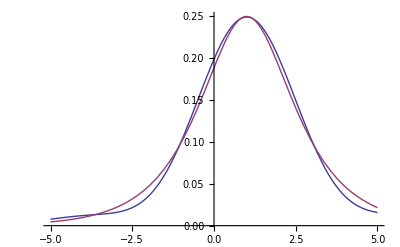

```mathematica
EdgeworthSeries[p_/;p≥2,y_]:=With[{z=(y-Cumulant[1]),σ=√Cumulant[2]},PDF[NormalDistribution[0,σ],z](1+Sum[σ^s/(2^(s/2+r)s!)HermiteH[s+2r,z/(√2 σ)]BellY[s,r,Table[Cumulant[k]/((k-1)k σ^(2k-2)),{k,3,p}]],{s,p-2},{r,s}])]
dist=SechDistribution[1,2];
pdf=MomentEvaluate[EdgeworthSeries[4,y],dist]
Plot[{pdf,PDF[dist,y]},{y,-5,5},PlotRange->All]
```

## Raw Moments of A

沒有答案可以對，不能確定是不是對的

```mathematica
s0=100;
K=120;
r=0.1;
s=0.3;
T=1;
n=50;

dt=T/n;

(* 要計算 A 的幾階 moment *)
k=12;

(* F1 LowerDiagonalMatrix 抄過來的 *)
LowerDiagonalMatrix[f_,n_Integer?NonNegative]:=Array[If[#≥#2,f[##],0]&,{n,n}];

(* 給出 x 的 raw moments 和二項式矩陣 *)
distx=LogNormalDistribution[(r-s^2/2)dt, s √dt];
binomatrix=LowerDiagonalMatrix[Binomial[#1-1,#2-1]&,k+1];
rawx=Table[Moment[distx, i], {i, 0, k}]//DiagonalMatrix;

(* 用矩陣乘法計算 A 的各階 raw moments，用 Take 把零階砍掉 *)
rawa=Take[(s0/(n+1))^Range[0, k](MatrixPower[binomatrix.rawx, n].Table[1, {k+1}]), -k]
```

{105.173,11406.5,1.27644×10^6,1.47473×10^8,1.76014×10^10,2.17161×10^12,2.77134×10^14,3.66062×10^16,5.00802×10^18,7.10096×10^20,1.04426×10^23,1.59384×10^25}

## Raw Moments & Cumulants of Lognormal Random Variables

合了前兩階 raw moments 的近似 A 的 lognormal distribution

{105.173,11406.5,1.2757×10^6,1.47126×10^8,1.74975×10^10,2.1459×10^12,2.71388×10^14,3.53929×10^16,4.75979×10^18,6.60095×10^20,9.43998×10^22,1.39214×10^25}

{105.173,345.198,3434.39,61262.9,1.61276×10^6,5.6726×10^7,2.51134×10^9,1.34511×10^11,8.47548×10^12,6.15194×10^14,5.05336×10^16,4.30544×10^18}

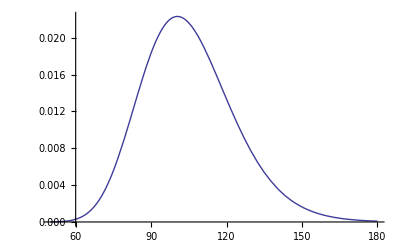

```mathematica
dd=LogNormalDistribution[Log[rawa[[1]]^2/(√rawa[[2]])], √Log[rawa[[2]]/rawa[[1]]^2]];
Table[Moment[dd, i], {i, k}]
Table[Cumulant[dd, i], {i, k}]
Plot[PDF[dd, x], {x, 50, 180}, PlotRange->All]
```

## Evaluate Cumulants With Raw Moments

前幾項對 wiki 確定是對的。
有內建的 MomentConvert 但不知道怎麼套用所以只能拿來對答案。

```mathematica
rawtest={r1, r2, r3, r4, r5, r6, r7, r8, r9, r10, r11, r12, r13, r14, r15, r16, r17, r18, r19, r20};
cum={rawtest[[1]]};
For[i=2, i≤k, 
AppendTo[cum, rawtest[[i]]-Sum[Binomial[i-1, p-1]cum[[p]]rawtest[[i-p]]//Expand, {p, 1, i-1}]];
i++]

cum//TableForm

MomentConvert[Cumulant[5], Moment]
```

r1
-r1^2+r2
2 r1^3-3 r1 r2+r3
-6 r1^4+12 r1^2 r2-3 r2^2-4 r1 r3+r4
24 r1^5-60 r1^3 r2+30 r1 r2^2+20 r1^2 r3-10 r2 r3-5 r1 r4+r5
-120 r1^6+360 r1^4 r2-270 r1^2 r2^2+30 r2^3-120 r1^3 r3+120 r1 r2 r3-10 r3^2+30 r1^2 r4-15 r2 r4-6 r1 r5+r6
720 r1^7-2520 r1^5 r2+2520 r1^3 r2^2-630 r1 r2^3+840 r1^4 r3-1260 r1^2 r2 r3+210 r2^2 r3+140 r1 r3^2-210 r1^3 r4+210 r1 r2 r4-35 r3 r4+42 r1^2 r5-21 r2 r5-7 r1 r6+r7
-5040 r1^8+20160 r1^6 r2-25200 r1^4 r2^2+10080 r1^2 r2^3-630 r2^4-6720 r1^5 r3+13440 r1^3 r2 r3-5040 r1 r2^2 r3-1680 r1^2 r3^2+560 r2 r3^2+1680 r1^4 r4-2520 r1^2 r2 r4+420 r2^2 r4+560 r1 r3 r4-35 r4^2-336 r1^3 r5+336 r1 r2 r5-56 r3 r5+56 r1^2 r6-28 r2 r6-8 r1 r7+r8
40320 r1^9-181440 r1^7 r2+272160 r1^5 r2^2-151200 r1^3 r2^3+22680 r1 r2^4+60480 r1^6 r3-151200 r1^4 r2 r3+90720 r1^2 r2^2 r3-7560 r2^3 r3+20160 r1^3 r3^2-15120 r1 r2 r3^2+560 r3^3-15120 r1^5 r4+30240 r1^3 r2 r4-11340 r1 r2^2 r4-7560 r1^2 r3 r4+2520 r2 r3 r4+630 r1 r4^2+3024 r1^4 r5-4536 r1^2 r2 r5+756 r2^2 r5+1008 r1 r3 r5-126 r4 r5-504 r1^3 r6+504 r1 r2 r6-84 r3 r6+72 r1^2 r7-36 r2 r7-9 r1 r8+r9
-362880 r1^10+r10+1814400 r1^8 r2-3175200 r1^6 r2^2+2268000 r1^4 r2^3-567000 r1^2 r2^4+22680 r2^5-604800 r1^7 r3+1814400 r1^5 r2 r3-1512000 r1^3 r2^2 r3+302400 r1 r2^3 r3-252000 r1^4 r3^2+302400 r1^2 r2 r3^2-37800 r2^2 r3^2-16800 r1 r3^3+151200 r1^6 r4-378000 r1^4 r2 r4+226800 r1^2 r2^2 r4-18900 r2^3 r4+100800 r1^3 r3 r4-75600 r1 r2 r3 r4+4200 r3^2 r4-9450 r1^2 r4^2+3150 r2 r4^2-30240 r1^5 r5+60480 r1^3 r2 r5-22680 r1 r2^2 r5-15120 r1^2 r3 r5+5040 r2 r3 r5+2520 r1 r4 r5-126 r5^2+5040 r1^4 r6-7560 r1^2 r2 r6+1260 r2^2 r6+1680 r1 r3 r6-210 r4 r6-720 r1^3 r7+720 r1 r2 r7-120 r3 r7+90 r1^2 r8-45 r2 r8-10 r1 r9
3628800 r1^11-11 r1 r10+r11-19958400 r1^9 r2+39916800 r1^7 r2^2-34927200 r1^5 r2^3+12474000 r1^3 r2^4-1247400 r1 r2^5+6652800 r1^8 r3-23284800 r1^6 r2 r3+24948000 r1^4 r2^2 r3-8316000 r1^2 r2^3 r3+415800 r2^4 r3+3326400 r1^5 r3^2-5544000 r1^3 r2 r3^2+1663200 r1 r2^2 r3^2+369600 r1^2 r3^3-92400 r2 r3^3-1663200 r1^7 r4+4989600 r1^5 r2 r4-4158000 r1^3 r2^2 r4+831600 r1 r2^3 r4-1386000 r1^4 r3 r4+1663200 r1^2 r2 r3 r4-207900 r2^2 r3 r4-138600 r1 r3^2 r4+138600 r1^3 r4^2-103950 r1 r2 r4^2+11550 r3 r4^2+332640 r1^6 r5-831600 r1^4 r2 r5+498960 r1^2 r2^2 r5-41580 r2^3 r5+221760 r1^3 r3 r5-166320 r1 r2 r3 r5+9240 r3^2 r5-41580 r1^2 r4 r5+13860 r2 r4 r5+2772 r1 r5^2-55440 r1^5 r6+110880 r1^3 r2 r6-41580 r1 r2^2 r6-27720 r1^2 r3 r6+9240 r2 r3 r6+4620 r1 r4 r6-462 r5 r6+7920 r1^4 r7-11880 r1^2 r2 r7+1980 r2^2 r7+2640 r1 r3 r7-330 r4 r7-990 r1^3 r8+990 r1 r2 r8-165 r3 r8+110 r1^2 r9-55 r2 r9
-39916800 r1^12+132 r1^2 r10-12 r1 r11+r12+239500800 r1^10 r2-66 r10 r2-538876800 r1^8 r2^2+558835200 r1^6 r2^3-261954000 r1^4 r2^4+44906400 r1^2 r2^5-1247400 r2^6-79833600 r1^9 r3+319334400 r1^7 r2 r3-419126400 r1^5 r2^2 r3+199584000 r1^3 r2^3 r3-24948000 r1 r2^4 r3-46569600 r1^6 r3^2+99792000 r1^4 r2 r3^2-49896000 r1^2 r2^2 r3^2+3326400 r2^3 r3^2-7392000 r1^3 r3^3+4435200 r1 r2 r3^3-92400 r3^4+19958400 r1^8 r4-69854400 r1^6 r2 r4+74844000 r1^4 r2^2 r4-24948000 r1^2 r2^3 r4+1247400 r2^4 r4+19958400 r1^5 r3 r4-33264000 r1^3 r2 r3 r4+9979200 r1 r2^2 r3 r4+3326400 r1^2 r3^2 r4-831600 r2 r3^2 r4-2079000 r1^4 r4^2+2494800 r1^2 r2 r4^2-311850 r2^2 r4^2-415800 r1 r3 r4^2+11550 r4^3-3991680 r1^7 r5+11975040 r1^5 r2 r5-9979200 r1^3 r2^2 r5+1995840 r1 r2^3 r5-3326400 r1^4 r3 r5+3991680 r1^2 r2 r3 r5-498960 r2^2 r3 r5-332640 r1 r3^2 r5+665280 r1^3 r4 r5-498960 r1 r2 r4 r5+55440 r3 r4 r5-49896 r1^2 r5^2+16632 r2 r5^2+665280 r1^6 r6-1663200 r1^4 r2 r6+997920 r1^2 r2^2 r6-83160 r2^3 r6+443520 r1^3 r3 r6-332640 r1 r2 r3 r6+18480 r3^2 r6-83160 r1^2 r4 r6+27720 r2 r4 r6+11088 r1 r5 r6-462 r6^2-95040 r1^5 r7+190080 r1^3 r2 r7-71280 r1 r2^2 r7-47520 r1^2 r3 r7+15840 r2 r3 r7+7920 r1 r4 r7-792 r5 r7+11880 r1^4 r8-17820 r1^2 r2 r8+2970 r2^2 r8+3960 r1 r3 r8-495 r4 r8-1320 r1^3 r9+1320 r1 r2 r9-220 r3 r9

24 Moment[1]^5-60 Moment[1]^3 Moment[2]+30 Moment[1] Moment[2]^2+20 Moment[1]^2 Moment[3]-10 Moment[2] Moment[3]-5 Moment[1] Moment[4]+Moment[5]

## Put Together

在這組參數下，由 FFT pricing 得到的正確答案為 2.36828545182878.....
而可以算到最準的 Edgeworth pricing 是取前 5 階 cumulants

```mathematica
Clear[dcum, r, d, μ, σ];

s0=100;
K=120;
r=0.1;
s=0.3;
T=1;
n=50;

dt=T/n;

k=5;(* 要計算 A 的幾階 moment？ k ≥ 2  *)


ini=TimeUsed[];

(* 定義二項式矩陣，定義 X 的分布，計算 X 的各階 moments *)
LowerDiagonalMatrix[f_,n_Integer?NonNegative]:=Array[If[#≥#2,f[##],0]&,{n,n}];
binomatrix=LowerDiagonalMatrix[Binomial[#1-1,#2-1]&,k+1];
distx=LogNormalDistribution[(r-s^2/2)dt, s √dt];
rawx=Table[Moment[distx, i], {i, 0, k}]//DiagonalMatrix;

(* 計算 A 的各階 moments，用 Take 把零階砍掉。計算 A 的 cumulants *)
rawa=Take[(s0/(n+1))^Range[0, k](MatrixPower[binomatrix.rawx, n].Table[1, {k+1}]), -k];
cuma={rawa[[1]]};
For[i=2, i≤k, AppendTo[cuma, rawa[[i]]-Sum[Binomial[i-1, p-1]cuma[[p]]rawa[[i-p]]//Expand, {p, 1, i-1}]];i++]

(* 定義 edgeworth expansion 的第一項，即合了前兩階 raw moments 的 lognormal distribution *)
dd=LogNormalDistribution[Log[rawa[[1]]^2/(√rawa[[2]])], √Log[rawa[[2]]/rawa[[1]]^2]];
g[x_]:=PDF[dd, x];
cumb=Table[Cumulant[dd, i], {i, k}];
dcum=cuma-cumb;

(* 計算 Edgeworth expansion 係數，最後用 Take[] 砍了零階 moment *)
Series[ⅇ^x, {x, 0, k}]//Normal;
%/.x->Sum[dcum[[r]](-d)^r/(r!), {r, 1, k}];
aaa=Take[CoefficientList[%, d], {2, k+1}];


If[k≤9, (* 懶人數值積分，k>9 會出問題 *)
ⅇ^(-r T)NIntegrate[Max[x-K, 0](g[x] + aaa.Table[D[g[x], {x, i}], {i, k}]), {x, 0, ∞}]
]

tt={Probability[x>K, x\[Distributed]dd], Table[D[g[x], {x, i}]/.x->K, {i, 0, k-2}]}//Flatten;
ⅇ^(-r T)(NIntegrate[Max[x-K, 0]g[x], {x, 0, ∞}] + aaa.tt)

TimeUsed[]-ini

(* k 設大一點就可以看出 Edgeworth 係數發散 *)
aaa
tt
```

2.37094

2.37094

0.171

{-1.42109×10^-14,6.36646×10^-12,-124.53,1357.75,-12849.8}

{0.200454,0.0133267,-0.000643208,6.28881×10^-6,2.74963×10^-6}

## Bug?

```mathematica
(* 這三個式子算出來答案應該要一樣，結果只有第二行算出來是對的 *)
Expectation[Max[x-K, 0], x\[Distributed]dd]
NIntegrate[Max[x-K, 0]g[x], {x, 0, ∞}]
Integrate[Max[x-K, 0]g[x], {x, K, ∞}]
```

95.9455

2.56699

95.9455

```mathematica
LogNormalDistribution[Log[rawa[[1]]^2/(√rawa[[2]])], √Log[rawa[[2]]/rawa[[1]]^2]]
Plot[{Max[x-K, 0], g[x]}, {x, 0, 200}, PlotRange->{0, 0.025}]
```

```mathematica
PDF[LogNormalDistribution[4.640238138022217,0.1753017040474435], x]
```

Piecewise[{{(2.27575 ⅇ^(-16.2704 (-4.64024+Log[x])^2))/x, x>0}, {0, True}}]

```mathematica
Integrate[(2.275746733719504 ⅇ^(-16.270381225434658 (-4.640238138022217+Log[x])^2))/x(x-K), {x, K, ∞}]
```

2.56699+1.15235×10^-12 ⅈ